# Programa 4 CI 2GDL MÉTODO ALGEBRÁICO

Se obtienen las ecuaciones de cinemática directa a partir de la tabla de Denavit-Hartenberg.

## FUNCIONES

```mathematica
(*FUNCIONES DE Matrices de Rotación 3x3 PARA CUALQUIER VARIABLE *)
Rx[α_]:={{1,0,0},{0,Cos[α], -Sin[α]}, {0,Sin[α], Cos[α]}};   
Ry[ϕ_]:={{Cos[ϕ],0,Sin[ϕ]},{0,1,0}, {-Sin[ϕ],0,Cos[ϕ]}};  
Rz[θ_]:={{Cos[θ], -Sin[θ],0},{Sin[θ], Cos[θ],0},{0,0,1}};
(*FUNCIONES de Matrices HOMEGENEAS de Traslación y Rotación 4x4 PARA CUALQUIER VARIABLE *)
Tx[x_]:={{1,0,0,x},{0,1,0,0},{0,0,1,0},{0,0,0,1}}
Ty[y_]:={{1,0,0,0},{0,1,0,y},{0,0,1,0},{0,0,0,1}}
Tz[z_]:={{1,0,0,0},{0,1,0,0},{0,0,1,z},{0,0,0,1}}

Qx[α_]:={{1,0,0,0},{0,Cos[α], -Sin[α], 0},{0, Sin[α], Cos[α],0},{0,0,0,1}}
Qy[ϕ_]:={{Cos[ϕ], 0, Sin[ϕ],0},{0,1,0,0},{-Sin[ϕ],0,Cos[ϕ],0},{0,0,0,1}}
Qz[θ_]:={{Cos[θ], -Sin[θ],0,0},{Sin[θ], Cos[θ],0,0},{0,0,1,0},{0,0,0,1}}
(*FUNCIONES de Matrices HOMEGENEAS De Denavit-Hartenberg *)

Q[θ_, d_, a_, α_]:=Qz[θ].Tz[d].Tx[a].Qx[α]

Ma=Q[θ1, d1, a1, α1];
Ma//MatrixForm
(*FUNCIONES ADICIONALES *)
n={0,0,0,1};
T3D[P_]:={P⟦1⟧,P⟦2⟧,P⟦3⟧ }
M3D[Q_]:={{Q⟦1,1⟧,Q⟦1,2⟧, Q⟦1,3⟧ },{Q⟦2,1⟧,Q⟦2,2⟧, Q⟦2,3⟧},{Q⟦3,1⟧,Q⟦3,2⟧, Q⟦3,3⟧}}
T={{NX, OX, AX},{NY, OY, AY},{NZ, OZ, AZ}};
T//MatrixForm
(*Función para la evolución de las variables articulares*)
Grafica[tabla_, rojo_,verde_,azul_,EjeX_,EjeY_]:=ListPlot[tabla,ImageSize->300, Joined->True, PlotStyle->{AbsoluteThickness[6], RGBColor[rojo,verde,azul]},BaseStyle->{14,FontFamily->"Arial"}, Frame->True, FrameLabel->{EjeX,EjeY},GridLines->Automatic, PlotRange->All];
```

(Cos[θ1] | -Cos[α1] Sin[θ1] | Sin[α1] Sin[θ1] | a1 Cos[θ1]
Sin[θ1] | Cos[α1] Cos[θ1] | -Cos[θ1] Sin[α1] | a1 Sin[θ1]
0 | Sin[α1] | Cos[α1] | d1
0 | 0 | 0 | 1)

(NX | OX | AX
NY | OY | AY
NZ | OZ | AZ)

## CINEMÁTICA DIRECTA 2 GDL DENAVIT-HARTENBERG

## DH 14- OBTENER LAS MATRICES ^(i-1)A_i

```mathematica
Underoverscript[a, 1, 0]=Q[θ1, 0,ℓ1, 0];
Underoverscript[a, 2, 1]=Q[θ2, 0,ℓ2,0];
```

## DH 15- OBTENER LAS MATRICES ^0 A_6=^0 A_1.^1 A_2.^2 A_3.....

```mathematica
Underoverscript[a, 2, 0]=Underoverscript[a, 1, 0].Underoverscript[a, 2, 1]//Simplify;
Underoverscript[a, 2, 0]//MatrixForm
```

(Cos[θ1+θ2] | -Sin[θ1+θ2] | 0 | ℓ1 Cos[θ1]+ℓ2 Cos[θ1+θ2]
Sin[θ1+θ2] | Cos[θ1+θ2] | 0 | ℓ1 Sin[θ1]+ℓ2 Sin[θ1+θ2]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

## DH 16- Vector de Posición del Efector Final y SubMatriz de Orientación

### Vector de Posición

```mathematica
X=Underoverscript[a, 2, 0]⟦1,4⟧//Simplify
Y=Underoverscript[a, 2, 0]⟦2,4⟧//Simplify
Z=Underoverscript[a, 2, 0]⟦3,4⟧//Simplify
```

ℓ1 Cos[θ1]+ℓ2 Cos[θ1+θ2]

ℓ1 Sin[θ1]+ℓ2 Sin[θ1+θ2]

0

### SubMatriz de Rotación

```mathematica
NX=Underoverscript[a, 2, 0]⟦1,1⟧//FullSimplify;
OX=Underoverscript[a, 2, 0]⟦1,2⟧//FullSimplify;
AX=Underoverscript[a, 2, 0]⟦1,3⟧//FullSimplify;

NY=Underoverscript[a, 2, 0]⟦2,1⟧//FullSimplify;
OY=Underoverscript[a, 2, 0]⟦2,2⟧//FullSimplify;
AY=Underoverscript[a, 2, 0]⟦2,3⟧//FullSimplify;

NZ=Underoverscript[a, 2, 0]⟦3,1⟧//FullSimplify;
OZ=Underoverscript[a, 2, 0]⟦3,2⟧//FullSimplify;
AZ=Underoverscript[a, 2, 0]⟦3,3⟧//FullSimplify;
```

## CINEMÁTICA IVERSA POR MÉTODO ALGEBRAICO

### SOLUCIÓN THETA2

```mathematica
(*Cómo paso 1. se eleve al cudrado a x^2 y a y^2*)
Xc=X^2;
Yc=Y^2;
SumXYc=Xc+Yc//FullSimplify;
SolC2=Solve[SumXYc==x^2+y^2, Cos[θ2]]//Flatten;
C2=Cos[θ2]/.SolC2;
S2=√(1-C2^2);
t2=ArcTan[C2,S2]   (*Función ArcTan2[Y,_X], unción ArcTan2[Sen,_Cos]*)
```

ArcTan[(x^2+y^2-ℓ1^2-ℓ2^2)/(2 ℓ1 ℓ2),√(1-((x^2+y^2-ℓ1^2-ℓ2^2)^2)/(4 ℓ1^2 ℓ2^2))]

### Solución theta 1

```mathematica
(*SE TOMAN 2 ECUACIONES X,Y Y DOS INCOGNITAS COS[θ1],SIN[θ1]*)
```

```mathematica
Xe=X//TrigExpand;
Ye=Y//TrigExpand;
SolC1S1=Solve[{Xe==x,Ye==y},{Cos[θ1],Sin[θ1]}]//Flatten//Simplify;
C1=Cos[θ1]/.SolC1S1⟦1⟧;
S1=Sin[θ1]/.SolC1S1⟦2⟧;
t1=ArcTan[C1,S1]
```

ArcTan[(x ℓ1+x ℓ2 Cos[θ2]+y ℓ2 Sin[θ2])/(ℓ1^2+ℓ2^2+2 ℓ1 ℓ2 Cos[θ2]),(y ℓ1+y ℓ2 Cos[θ2]-x ℓ2 Sin[θ2])/(ℓ1^2+ℓ2^2+2 ℓ1 ℓ2 Cos[θ2])]

## TRAYECTORIA

```mathematica
ℓ1=10;
ℓ2=15;
tf=100;
aa=5;
Cero={0,0,0};
For[t=0, t≤tf, t+=1,
Perfil=10*(t/tf)^3-15*(t/tf)^4 +6*(t/tf)^5;Trayectoria[t]={
2*aa*Cos[2*Pi*Perfil]-aa*Cos[4*Pi*Perfil]+7,
2*aa*Sin[4*Pi*Perfil]-aa*Sin[4*Pi*Perfil]+12,
0
}
];
Tablaxyz=Table[{Trayectoria[t]⟦1⟧,Trayectoria[t]⟦2⟧,Trayectoria[t]⟦3⟧},{t,0,tf,1}];
TrayectoriaEF=Line[Tablaxyz];
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}
},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-45,40}, {-40,40},{-0,1}}
]
```

-Graphics3D-

Table::iterb: Iterator {t,0,tf,1} does not have appropriate bounds.

Line[Table[{Trayectoria[t]⟦1⟧,Trayectoria[t]⟦2⟧,Trayectoria[t]⟦3⟧},{t,0,tf,1}]]

## SIMULACIÓN

```mathematica
Tabla=Table[{x[t],y[t],z[t]},{t,0,tf,1}];   
TrayectoriaEF=Line[Tabla];
Eslabon1=Line[{Cero,T3D[Underoverscript[a, 1, 0].n]}];
Eslabon2=Line[{T3D[Underoverscript[a, 1, 0].n],T3D[Underoverscript[a, 2, 0].n]}];
Eslabon3=Line[{T3D[Underoverscript[a, 2, 0].n],T3D[Underoverscript[a, 3, 0].n]}];
Eslabon4=Line[{T3D[Underoverscript[a, 3, 0].n],T3D[Underoverscript[a, 4, 0].n]}];
Eslabon5=Line[{T3D[Underoverscript[a, 4, 0].n],T3D[Underoverscript[a, 5, 0].n]}];
Eslabon6=Line[{T3D[Underoverscript[a, 5, 0].n],T3D[Underoverscript[a, 6, 0].n]}];

Animate[
Graphics3D[
{
{AbsoluteThickness[1],RGBColor[1,0,0],TrayectoriaEF}, 
{AbsoluteThickness[5],RGBColor[1,0,0.5],Eslabon1/.VartArt[t]}, 
{AbsoluteThickness[4],RGBColor[1,0.7,0],Eslabon2/.VartArt[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0.5],Eslabon3/.VartArt[t]}, 
{AbsoluteThickness[2],RGBColor[1,0,1],Eslabon4/.VartArt[t]}, 
{AbsoluteThickness[3],RGBColor[1,1,0],Eslabon5/.VartArt[t]}, 
{AbsoluteThickness[2],RGBColor[0,1,1],Eslabon6/.VartArt[t]}
},
Axes->True, AxesLabel->{x,y,z},AxesStyle->{Red, Green, Blue}, BaseStyle->{24, FontFamily["Arial"]}, ImageSize->300, PlotRange->{{-150,150}, {-150,150},{-20,150}}
],{t,0,tf,1}
]
```

## EVOLUCIÓN DE LAS VARIABLES ARTICULARES

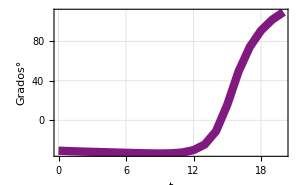

```mathematica
Tabla1=Table[{t, (θ1/.VartArt[t])/Degree},{t,0,tf,1}];
Theta1=Grafica[Tabla1,.5,.1,.5,"t", "Grados°"]
```

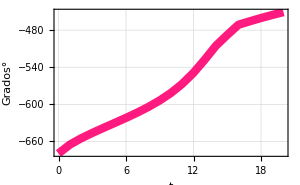

```mathematica
Tabla2=Table[{t, (θ2/.VartArt[t])/Degree},{t,0,tf,1}];
Theta2=Grafica[Tabla2,1,.1,.5,"t", "Grados°"]
```

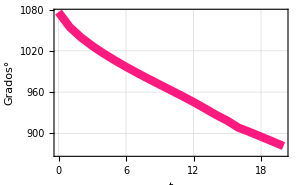

```mathematica
Tabla3=Table[{t, (θ3/.VartArt[t])/Degree},{t,0,tf,1}];
Theta3=Grafica[Tabla3,1,.1,.5,"t", "Grados°"]
```

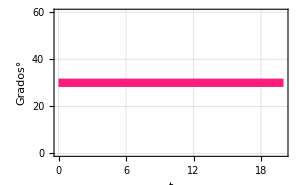

```mathematica
Tabla4=Table[{t, (θ4/.VartArt[t])/Degree},{t,0,tf,1}];
Theta4=Grafica[Tabla4,1,.1,.5,"t", "Grados°"]
```

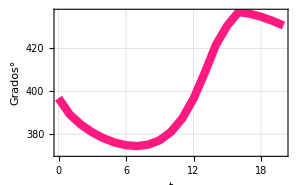

```mathematica
Tabla5=Table[{t, (θ5/.VartArt[t])/Degree},{t,0,tf,1}];
Theta5=Grafica[Tabla5,1,.1,.5,"t", "Grados°"]
```

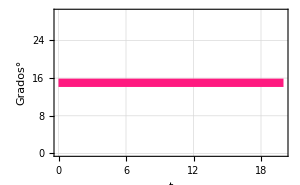

```mathematica
Tabla6=Table[{t, (θ6/.VartArt[t])/Degree},{t,0,tf,1}];
Theta6=Grafica[Tabla6,1,.1,.5,"t", "Grados°"]
```